```mathematica
r = Range[10,10000,10];
r1=Range[10,1000,10];
f=PrimePi[r];
g=N[LogIntegral[r]];
g1=N[LogIntegral[r1]];
f1=PrimePi[r1];
h=f/(r/Log[r]);
h1=f1/(r1/Log[r1]);
l=f-r/Log[r];
l1=f1-r1/Log[r1];
j=r/Power[Log[r],2];
k=r/Log[r];
k1=r1/Log[r1];
d = 1/Log[r1];
c=f1/r1;
dm=1/(Log[r1]-1);
```

Most of these functions are just for playing around with, some might not be used.

```mathematica
PrimePi[1000]
```

168

```mathematica
N[1000/Log[1000]]
```

144.765

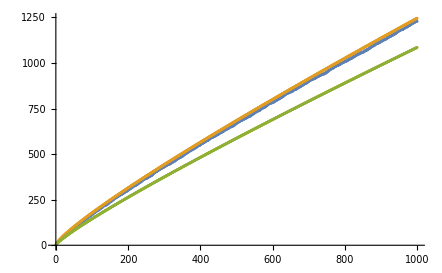

```mathematica
ListPlot[{f,g,k}]
```

These graphs shows the actual number of primes(the blue line) to the approximation of this number given by li(x) (red line) and x/ln(x) (the green line). As the number or primes keeps growing we can see that this approximation seems to squeezing to the value of pi(x)

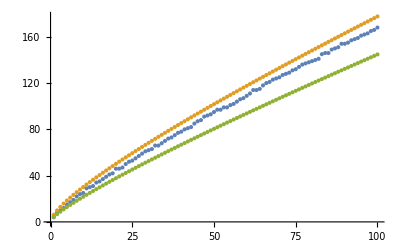

```mathematica
ListPlot[{f1,g1,k1}]
```

This graph shows the density of primes less than x using Pi(x)/x as the blue line and the approximating measurements 1/log(x) and 1/log(x)-1(the green line). This is using a smaller range because as x gets large, these lines will become closer.

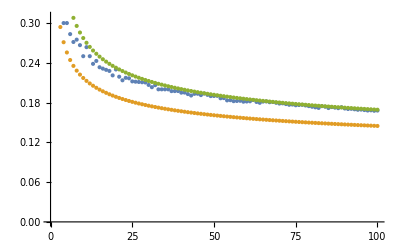

```mathematica
ListPlot[{c,d,dm}]
```